```mathematica
a=0.2;
b=0.1;
```

```mathematica
f[t_]:={0.5+a Cos[t](1-Sin[t]),0.5+ b Sin[t](1+Cos[t])}
```

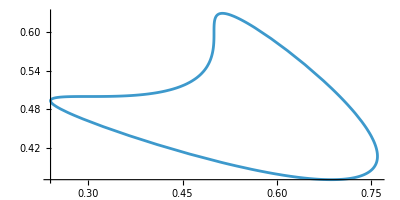

```mathematica
ParametricPlot[f[t],{t,0,2π}]
```

```mathematica
g[x_]:=x[[1]]+2x[[2]]
```

```mathematica
Integrate[g[f[t]],{t,0,1}]
```

1.76023